## Poisson-equation approach, Series treatment -- (0, 2Pi) integration, all periodic BC

```mathematica
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qx0-bmu(Cos[theta1]+Cos[theta2]))
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qx1-bmu^2(Cos[theta1]+Cos[theta2])^2+Qx0 bmu(Cos[theta1]+Cos[theta2]))
```

```mathematica
(*Clear[H0,H0c,H0s,I0cch,I0csh,I0sch,I0ssh,A0c,dA0c]*)
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
pv10[bJx_,bmux_,theta1_,theta2_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,theta1_,theta2_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,1,nmax},{j,0,jmax}]

H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
A1[0,j_,theta1_]:=Integrate[h1[0,j](theta1-t1),{t1,0,theta1}]
A1[n_,j_,theta1_]:=2/n Integrate[h1[n,j]Sinh[n/2(theta1-t1)],{t1,0,theta1}]-2Cosh[n/2 theta1]/(n Sinh[n Pi])Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
dA1[0,j_,theta1_]:=Integrate[h1[0,j],{t1,0,theta1}]
dA1[n_,j_,theta1_]:=Integrate[h1[n,j]Cosh[n/2(theta1-t1)],{t1,0,theta1}]-2Sinh[n/2 theta1]/Sinh[n Pi]Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
```

```mathematica
Flatten[Table[{n,j,H0[0,j,t1_]:=Release[H0[0,j,t1]]},{j,0,10}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,H0c[n,j,t1_]:=Release[H0c[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,H0s[n,j,t1_]:=Release[H0s[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0cch[n,j,t1_]:=Release[I0cch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0sch[n,j,t1_]:=Release[I0sch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0csh[n,j,t1_]:=Release[I0csh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0ssh[n,j,t1_]:=Release[I0ssh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,A0c[n,j,theta1_]:=Release[A0c[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,dA0c[0,j,theta1_]:=Release[dA0c[0,j,theta1]]},{j,0,10}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,h1[n,j]=H1[n,j,t1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm;
```

0 | 0 | -0.5+1. Qx1-1. Cos[t1]^2
0 | 1 | -0.5+9.74543×10^-18 Cos[t1]+3.89817×10^-17 Cos[t1]^2-0.5 Cos[2. t1]
0 | 2 | 0.0795775 (-3.14159+3.14159 Qx1+6.12323×10^-17 Cos[t1]+(-2.35619-1.22465×10^-16 Qx1) Cos[2. t1]+6.12323×10^-17 Cos[3. t1]+3.06162×10^-17 Cos[4. t1])
0 | 3 | 0.0265258 (2.44929×10^-16 Cos[t1]^4+1.22465×10^-16 Cos[t1]^2 (-0.5+1. Cos[2. t1])+1.53081×10^-17 Cos[3. t1]-1.22465×10^-16 Cos[t1] (-0.125-0.5 Qx1+(-0.75+1. Qx1) Cos[2. t1]-0.25 Cos[4. t1])-4.71239 (Cos[0.5 t1]^2-1. Sin[0.5 t1]^2)^2)
0 | 4 | 0.00663146 (-2.35619+2.35619 Qx1+6.12323×10^-17 Cos[t1]+(-1.9635-1.22465×10^-16 Qx1) Cos[2. t1]+9.18485×10^-17 Cos[3. t1]+7.65404×10^-17 Cos[4. t1]-3.06162×10^-17 Qx1 Cos[4. t1]+3.06162×10^-17 Cos[5. t1]+7.65404×10^-18 Cos[6. t1])
0 | 5 | -0.00260417+(2.79166×10^-19-2.0303×10^-19 Qx1) Cos[t1]-0.00260417 Cos[(2.+0. ⅈ) t1]+2.08106×10^-19 Cos[(3.+0. ⅈ) t1]-1.01515×10^-19 Qx1 Cos[(3.+0. ⅈ) t1]+1.21818×10^-19 Cos[(4.+0. ⅈ) t1]+5.58332×10^-20 Cos[(5.+0. ⅈ) t1]-2.0303×10^-20 Qx1 Cos[(5.+0. ⅈ) t1]+2.0303×10^-20 Cos[(6.+0. ⅈ) t1]+5.07574×10^-21 Cos[(7.+0. ⅈ) t1]-3.6812×10^-20 Sin[(2.+0. ⅈ) t1]+7.3624×10^-20 Sin[(3.+0. ⅈ) t1]-5.5218×10^-20 Sin[(4.+0. ⅈ) t1]+9.20299×10^-21 Sin[(5.+0. ⅈ) t1]
0 | 6 | 0.000221049 (-1.9635+1.9635 Qx1+1.91351×10^-16 Cos[t1]+(-1.71806-1.14811×10^-16 Qx1) Cos[(2.+0. ⅈ) t1]+1.60735×10^-16 Cos[(3.+0. ⅈ) t1]+9.95026×10^-17 Cos[(4.+0. ⅈ) t1]-4.59243×10^-17 Qx1 Cos[(4.+0. ⅈ) t1]+5.35783×10^-17 Cos[(5.+0. ⅈ) t1]+2.29621×10^-17 Cos[(6.+0. ⅈ) t1]-7.65404×10^-18 Qx1 Cos[(6.+0. ⅈ) t1]+7.65404×10^-18 Cos[(7.+0. ⅈ) t1]+1.91351×10^-18 Cos[(8.+0. ⅈ) t1]-2.77556×10^-17 Sin[(2.+0. ⅈ) t1]+2.77556×10^-17 Sin[(3.+0. ⅈ) t1]-4.16334×10^-17 Sin[(4.+0. ⅈ) t1]+6.93889×10^-18 Sin[(5.+0. ⅈ) t1]+1.73472×10^-18 Sin[(6.+0. ⅈ) t1]+8.67362×10^-19 Sin[(7.+0. ⅈ) t1])
0 | 7 | -0.0000542535+(5.9217×10^-21-4.22979×10^-21 Qx1) Cos[t1]-0.0000542535 Cos[(2.+0. ⅈ) t1]+5.07574×10^-21 Cos[(3.+0. ⅈ) t1]-2.53787×10^-21 Qx1 Cos[(3.+0. ⅈ) t1]+3.38383×10^-21 Cos[(4.+0. ⅈ) t1]+1.93362×10^-21 Cos[(5.+0. ⅈ) t1]-8.45957×10^-22 Qx1 Cos[(5.+0. ⅈ) t1]+9.66808×10^-22 Cos[(6.+0. ⅈ) t1]+3.92766×10^-22 Cos[(7.+0. ⅈ) t1]-1.20851×10^-22 Qx1 Cos[(7.+0. ⅈ) t1]+1.20851×10^-22 Cos[(8.+0. ⅈ) t1]+3.02128×10^-23 Cos[(9.+0. ⅈ) t1]+3.5059×10^-21 Sin[t1]-8.76476×10^-22 Sin[(4.+0. ⅈ) t1]+2.19119×10^-22 Sin[(5.+0. ⅈ) t1]-1.09559×10^-22 Sin[(7.+0. ⅈ) t1]+6.84747×10^-24 Sin[(8.+0. ⅈ) t1]
0 | 8 | 3.9473×10^-6 (-1.71806+1.71806 Qx1+1.74129×10^-16 Cos[t1]+(-1.54625-1.07157×10^-16 Qx1) Cos[(2.+0. ⅈ) t1]+1.60735×10^-16 Cos[(3.+0. ⅈ) t1]+1.10984×10^-16 Cos[(4.+0. ⅈ) t1]-5.35783×10^-17 Qx1 Cos[(4.+0. ⅈ) t1]+6.88864×10^-17 Cos[(5.+0. ⅈ) t1]+3.68351×10^-17 Cos[(6.+0. ⅈ) t1]-1.53081×10^-17 Qx1 Cos[(6.+0. ⅈ) t1]+1.72216×10^-17 Cos[(7.+0. ⅈ) t1]+6.69729×10^-18 Cos[(8.+0. ⅈ) t1]-1.91351×10^-18 Qx1 Cos[(8.+0. ⅈ) t1]+1.91351×10^-18 Cos[(9.+0. ⅈ) t1]+4.78378×10^-19 Cos[(10.+0. ⅈ) t1]+5.55112×10^-17 Sin[t1]+6.93889×10^-18 Sin[(5.+0. ⅈ) t1]-3.46945×10^-18 Sin[(7.+0. ⅈ) t1]-8.67362×10^-19 Sin[(8.+0. ⅈ) t1])
0 | 9 | -6.78168×10^-7+(7.49025×10^-23-5.28723×10^-23 Qx1) Cos[t1]-6.78168×10^-7 Cos[(2.+0. ⅈ) t1]+6.9867×10^-23 Cos[(3.+0. ⅈ) t1]-3.52482×10^-23 Qx1 Cos[(3.+0. ⅈ) t1]+5.03546×10^-23 Cos[(4.+0. ⅈ) t1]+3.24158×10^-23 Cos[(5.+0. ⅈ) t1]-1.51064×10^-23 Qx1 Cos[(5.+0. ⅈ) t1]+1.8883×10^-23 Cos[(6.+0. ⅈ) t1]+9.54639×10^-24 Cos[(7.+0. ⅈ) t1]-3.7766×10^-24 Qx1 Cos[(7.+0. ⅈ) t1]+4.19622×10^-24 Cos[(8.+0. ⅈ) t1]+1.85025×10^-24 Cos[(9.+0. ⅈ) t1]-4.19622×10^-25 Qx1 Cos[(9.+0. ⅈ) t1]+4.19622×10^-25 Cos[(10.+0. ⅈ) t1]+1.04905×10^-25 Cos[(11.+0. ⅈ) t1]-6.08664×10^-24 Sin[(5.+0. ⅈ) t1]-3.80415×10^-25 Sin[(8.+0. ⅈ) t1]+9.51037×10^-26 Sin[(9.+0. ⅈ) t1]+1.1888×10^-26 Sin[(10.+0. ⅈ) t1]
0 | 10 | 4.38588×10^-8 (-1.54625+1.54625 Qx1+1.60735×10^-16 Cos[t1]+(-1.4174-1.00459×10^-16 Qx1) Cos[(2.+0. ⅈ) t1]+1.57865×10^-16 Cos[(3.+0. ⅈ) t1]+1.16605×10^-16 Cos[(4.+0. ⅈ) t1]-5.74053×10^-17 Qx1 Cos[(4.+0. ⅈ) t1]+7.89323×10^-17 Cos[(5.+0. ⅈ) t1]+4.78378×10^-17 Cos[(6.+0. ⅈ) t1]-2.1527×10^-17 Qx1 Cos[(6.+0. ⅈ) t1]+2.63108×10^-17 Cos[(7.+0. ⅈ) t1]+1.2677×10^-17 Cos[(8.+0. ⅈ) t1]-4.78378×10^-18 Qx1 Cos[(8.+0. ⅈ) t1]+5.89296×10^-18 Cos[(9.+0. ⅈ) t1]+1.91351×10^-18 Cos[(10.+0. ⅈ) t1]-4.78378×10^-19 Qx1 Cos[(10.+0. ⅈ) t1]+1.10919×10^-18 Cos[(11.+0. ⅈ) t1]+1.19594×10^-19 Cos[(12.+0. ⅈ) t1]-1.38778×10^-17 Sin[(5.+0. ⅈ) t1]+3.46945×10^-18 Sin[(7.+0. ⅈ) t1]+8.67362×10^-19 Sin[(8.+0. ⅈ) t1]-2.1684×10^-19 Sin[(9.+0. ⅈ) t1]+1.0842×10^-19 Sin[(10.+0. ⅈ) t1]-1.35525×10^-20 Sin[(11.+0. ⅈ) t1])
1 | 0 | H1[1,0,t1]
1 | 1 | H1[1,1,t1]
1 | 2 | H1[1,2,t1]
1 | 3 | H1[1,3,t1]
1 | 4 | H1[1,4,t1]
1 | 5 | H1[1,5,t1]
1 | 6 | H1[1,6,t1]
1 | 7 | H1[1,7,t1]
1 | 8 | H1[1,8,t1]
1 | 9 | H1[1,9,t1]
1 | 10 | H1[1,10,t1]
2 | 0 | H1[2,0,t1]
2 | 1 | H1[2,1,t1]
2 | 2 | H1[2,2,t1]
2 | 3 | H1[2,3,t1]
2 | 4 | H1[2,4,t1]
2 | 5 | H1[2,5,t1]
2 | 6 | H1[2,6,t1]
2 | 7 | H1[2,7,t1]
2 | 8 | H1[2,8,t1]
2 | 9 | H1[2,9,t1]
2 | 10 | H1[2,10,t1]
3 | 0 | H1[3,0,t1]
3 | 1 | H1[3,1,t1]
3 | 2 | H1[3,2,t1]
3 | 3 | H1[3,3,t1]
3 | 4 | H1[3,4,t1]
3 | 5 | H1[3,5,t1]
3 | 6 | H1[3,6,t1]
3 | 7 | H1[3,7,t1]
3 | 8 | H1[3,8,t1]
3 | 9 | H1[3,9,t1]
3 | 10 | H1[3,10,t1]
4 | 0 | H1[4,0,t1]
4 | 1 | H1[4,1,t1]
4 | 2 | H1[4,2,t1]
4 | 3 | H1[4,3,t1]
4 | 4 | H1[4,4,t1]
4 | 5 | H1[4,5,t1]
4 | 6 | H1[4,6,t1]
4 | 7 | H1[4,7,t1]
4 | 8 | H1[4,8,t1]
4 | 9 | H1[4,9,t1]
4 | 10 | H1[4,10,t1]
5 | 0 | H1[5,0,t1]
5 | 1 | H1[5,1,t1]
5 | 2 | H1[5,2,t1]
5 | 3 | H1[5,3,t1]
5 | 4 | H1[5,4,t1]
5 | 5 | H1[5,5,t1]
5 | 6 | H1[5,6,t1]
5 | 7 | H1[5,7,t1]
5 | 8 | H1[5,8,t1]
5 | 9 | H1[5,9,t1]
5 | 10 | H1[5,10,t1]
6 | 0 | H1[6,0,t1]
6 | 1 | H1[6,1,t1]
6 | 2 | H1[6,2,t1]
6 | 3 | H1[6,3,t1]
6 | 4 | H1[6,4,t1]
6 | 5 | H1[6,5,t1]
6 | 6 | H1[6,6,t1]
6 | 7 | H1[6,7,t1]
6 | 8 | H1[6,8,t1]
6 | 9 | H1[6,9,t1]
6 | 10 | H1[6,10,t1]
7 | 0 | H1[7,0,t1]
7 | 1 | H1[7,1,t1]
7 | 2 | H1[7,2,t1]
7 | 3 | H1[7,3,t1]
7 | 4 | H1[7,4,t1]
7 | 5 | H1[7,5,t1]
7 | 6 | H1[7,6,t1]
7 | 7 | H1[7,7,t1]
7 | 8 | H1[7,8,t1]
7 | 9 | H1[7,9,t1]
7 | 10 | H1[7,10,t1]
8 | 0 | H1[8,0,t1]
8 | 1 | H1[8,1,t1]
8 | 2 | H1[8,2,t1]
8 | 3 | H1[8,3,t1]
8 | 4 | H1[8,4,t1]
8 | 5 | H1[8,5,t1]
8 | 6 | H1[8,6,t1]
8 | 7 | H1[8,7,t1]
8 | 8 | H1[8,8,t1]
8 | 9 | H1[8,9,t1]
8 | 10 | H1[8,10,t1]
9 | 0 | H1[9,0,t1]
9 | 1 | H1[9,1,t1]
9 | 2 | H1[9,2,t1]
9 | 3 | H1[9,3,t1]
9 | 4 | H1[9,4,t1]
9 | 5 | H1[9,5,t1]
9 | 6 | H1[9,6,t1]
9 | 7 | H1[9,7,t1]
9 | 8 | H1[9,8,t1]
9 | 9 | H1[9,9,t1]
9 | 10 | H1[9,10,t1]
10 | 0 | H1[10,0,t1]
10 | 1 | H1[10,1,t1]
10 | 2 | H1[10,2,t1]
10 | 3 | H1[10,3,t1]
10 | 4 | H1[10,4,t1]
10 | 5 | H1[10,5,t1]
10 | 6 | H1[10,6,t1]
10 | 7 | H1[10,7,t1]
10 | 8 | H1[10,8,t1]
10 | 9 | H1[10,9,t1]
10 | 10 | H1[10,10,t1]

```mathematica
Flatten[Table[{n,j,da0[n,j]=dA0[n,j,theta1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm;
```

0 | 0 | dA0[0,0,theta1]
0 | 1 | dA0[0,1,theta1]
0 | 2 | dA0[0,2,theta1]
0 | 3 | dA0[0,3,theta1]
0 | 4 | dA0[0,4,theta1]
0 | 5 | dA0[0,5,theta1]
0 | 6 | dA0[0,6,theta1]
0 | 7 | dA0[0,7,theta1]
0 | 8 | dA0[0,8,theta1]
0 | 9 | dA0[0,9,theta1]
0 | 10 | dA0[0,10,theta1]
1 | 0 | dA0[1,0,theta1]
1 | 1 | dA0[1,1,theta1]
1 | 2 | dA0[1,2,theta1]
1 | 3 | dA0[1,3,theta1]
1 | 4 | dA0[1,4,theta1]
1 | 5 | dA0[1,5,theta1]
1 | 6 | dA0[1,6,theta1]
1 | 7 | dA0[1,7,theta1]
1 | 8 | dA0[1,8,theta1]
1 | 9 | dA0[1,9,theta1]
1 | 10 | dA0[1,10,theta1]
2 | 0 | dA0[2,0,theta1]
2 | 1 | dA0[2,1,theta1]
2 | 2 | dA0[2,2,theta1]
2 | 3 | dA0[2,3,theta1]
2 | 4 | dA0[2,4,theta1]
2 | 5 | dA0[2,5,theta1]
2 | 6 | dA0[2,6,theta1]
2 | 7 | dA0[2,7,theta1]
2 | 8 | dA0[2,8,theta1]
2 | 9 | dA0[2,9,theta1]
2 | 10 | dA0[2,10,theta1]
3 | 0 | dA0[3,0,theta1]
3 | 1 | dA0[3,1,theta1]
3 | 2 | dA0[3,2,theta1]
3 | 3 | dA0[3,3,theta1]
3 | 4 | dA0[3,4,theta1]
3 | 5 | dA0[3,5,theta1]
3 | 6 | dA0[3,6,theta1]
3 | 7 | dA0[3,7,theta1]
3 | 8 | dA0[3,8,theta1]
3 | 9 | dA0[3,9,theta1]
3 | 10 | dA0[3,10,theta1]
4 | 0 | dA0[4,0,theta1]
4 | 1 | dA0[4,1,theta1]
4 | 2 | dA0[4,2,theta1]
4 | 3 | dA0[4,3,theta1]
4 | 4 | dA0[4,4,theta1]
4 | 5 | dA0[4,5,theta1]
4 | 6 | dA0[4,6,theta1]
4 | 7 | dA0[4,7,theta1]
4 | 8 | dA0[4,8,theta1]
4 | 9 | dA0[4,9,theta1]
4 | 10 | dA0[4,10,theta1]
5 | 0 | dA0[5,0,theta1]
5 | 1 | dA0[5,1,theta1]
5 | 2 | dA0[5,2,theta1]
5 | 3 | dA0[5,3,theta1]
5 | 4 | dA0[5,4,theta1]
5 | 5 | dA0[5,5,theta1]
5 | 6 | dA0[5,6,theta1]
5 | 7 | dA0[5,7,theta1]
5 | 8 | dA0[5,8,theta1]
5 | 9 | dA0[5,9,theta1]
5 | 10 | dA0[5,10,theta1]
6 | 0 | dA0[6,0,theta1]
6 | 1 | dA0[6,1,theta1]
6 | 2 | dA0[6,2,theta1]
6 | 3 | dA0[6,3,theta1]
6 | 4 | dA0[6,4,theta1]
6 | 5 | dA0[6,5,theta1]
6 | 6 | dA0[6,6,theta1]
6 | 7 | dA0[6,7,theta1]
6 | 8 | dA0[6,8,theta1]
6 | 9 | dA0[6,9,theta1]
6 | 10 | dA0[6,10,theta1]
7 | 0 | dA0[7,0,theta1]
7 | 1 | dA0[7,1,theta1]
7 | 2 | dA0[7,2,theta1]
7 | 3 | dA0[7,3,theta1]
7 | 4 | dA0[7,4,theta1]
7 | 5 | dA0[7,5,theta1]
7 | 6 | dA0[7,6,theta1]
7 | 7 | dA0[7,7,theta1]
7 | 8 | dA0[7,8,theta1]
7 | 9 | dA0[7,9,theta1]
7 | 10 | dA0[7,10,theta1]
8 | 0 | dA0[8,0,theta1]
8 | 1 | dA0[8,1,theta1]
8 | 2 | dA0[8,2,theta1]
8 | 3 | dA0[8,3,theta1]
8 | 4 | dA0[8,4,theta1]
8 | 5 | dA0[8,5,theta1]
8 | 6 | dA0[8,6,theta1]
8 | 7 | dA0[8,7,theta1]
8 | 8 | dA0[8,8,theta1]
8 | 9 | dA0[8,9,theta1]
8 | 10 | dA0[8,10,theta1]
9 | 0 | dA0[9,0,theta1]
9 | 1 | dA0[9,1,theta1]
9 | 2 | dA0[9,2,theta1]
9 | 3 | dA0[9,3,theta1]
9 | 4 | dA0[9,4,theta1]
9 | 5 | dA0[9,5,theta1]
9 | 6 | dA0[9,6,theta1]
9 | 7 | dA0[9,7,theta1]
9 | 8 | dA0[9,8,theta1]
9 | 9 | dA0[9,9,theta1]
9 | 10 | dA0[9,10,theta1]
10 | 0 | dA0[10,0,theta1]
10 | 1 | dA0[10,1,theta1]
10 | 2 | dA0[10,2,theta1]
10 | 3 | dA0[10,3,theta1]
10 | 4 | dA0[10,4,theta1]
10 | 5 | dA0[10,5,theta1]
10 | 6 | dA0[10,6,theta1]
10 | 7 | dA0[10,7,theta1]
10 | 8 | dA0[10,8,theta1]
10 | 9 | dA0[10,9,theta1]
10 | 10 | dA0[10,10,theta1]

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

```mathematica
Qx0
```

0

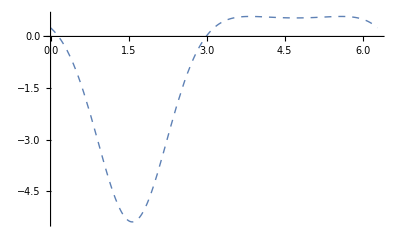

```mathematica
nmax=jmax=4;
myt2=Pi/2;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

```mathematica
t2=2;
{t2,pvx10[ t2,myt2,nmax]Exp[Cos[t2-myt2]],pvx20[ myt2,t2,nmax]Exp[Cos[t2-myt2]],pv10[1,1,t2,myt2]Exp[Cos[t2-myt2]],pv20[1,1,myt2,t2]Exp[Cos[t2-myt2]]}
```

{2,-5.56844,-3.04389,-2.88156,-2.88156}

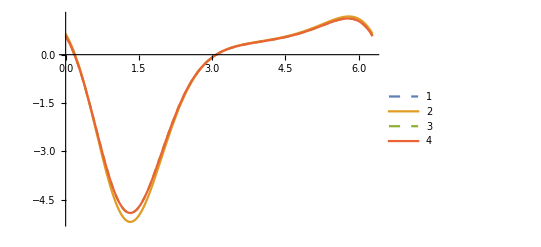

```mathematica
nmax=5;
bJ=bmu=1;
jmax=2;
myt2=Pi/3;
Plot[{pvx10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvx20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]],pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic]
```

```mathematica
Plot[{pvx10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic]
```

-Graphics-

```mathematica
myt1=Pi/4;
nmax
{myt1,pvx10[ myt1,myt2,nmax],pv10[1,1,myt1,myt2]}//N
```

1

{0.785398,-2.72992,-1.36244}

```mathematica
?pvx10
```

Global`pvx10

pvx10[theta1_,theta2_,nmax_]:=∑_(n=0)^nmax Release[dAxs0[n,theta1] Sin[n theta2]+dAxc0[n,theta1] Cos[n theta2]]

```mathematica
?pv10
```

Global`pv10

pv10[bJx_,bmux_,theta1_,theta2_]:=∑_(n=0)^nmax ∑_(j=0)^jmax (dA0s[n,j,theta1] Sin[n theta2]+dA0c[n,j,theta1] Cos[n theta2]/.{Qx0→0,bJ→bJx,bmu→bmux})

```mathematica
nmax
```

1

```mathematica
Table[{n,dAxs0[n,myt1]Sin[n myt2],Sum[dA0s[n,j,myt1],{j,0,5}]Sin[n myt2]},{n,0,5}]/.{bJ->1,bmu->1}//N
Table[{n,dAxc0[n,myt1]Cos[n myt2],Sum[dA0c[n,j,myt1],{j,0,5}]Cos[n myt2]},{n,0,5}]/.{bJ->1,bmu->1}//N
```

{{0.,0.,0.},{1.,0.,0.},{2.,0.063527,0.0635312},{3.,0.,0.},{4.,0.00205486,0.00203191},{5.,0.000254196,0.000242029}}

{{0.,-1.29487,-1.29452},{1.,-0.140181,-0.140104},{2.,0.0624458,0.0623889},{3.,0.0242948,0.0242388},{4.,0.000926934,0.000926101},{5.,0.0000144566,0.0000128112}}

```mathematica
n=0;
testp0=dAxs0[n,myt1]Sin[n myt2]+dAxc0[n,myt1]Cos[n myt2]//N;
n=1;
testp1=dAxs0[n,myt1]Sin[n myt2]+dAxc0[n,myt1]Cos[n myt2]//N;
n=2;
testp2=dAxs0[n,myt1]Sin[n myt2]+dAxc0[n,myt1]Cos[n myt2]//N;
Print["p0=",testp0]//N
Print["p1=",testp1+testp0]//N
Print["p2=",testp2+testp1+testp0]//N
pvx10[ myt1,myt2,0]//N
pvx10[ myt1,myt2,1]//N
pvx10[ myt1,myt2,2]//N
(*pvx10n[myt1,myt2,0]//N
pvx10n[myt1,myt2,1]//N
pvx10n[myt1,myt2,2]//N
pvx10n[myt1,myt2,3]//N*)
```

p0=-1.29487

p1=-1.43505

p2=-1.30908

-1.29487

-1.43505

-1.30908

```mathematica
n=1;Release[dAxs0[n,myt1]Sin[n myt2]+dAxc0[n,myt1]Cos[n myt2]]//N
n=2;Release[dAxs0[n,myt1]Sin[n myt2]+dAxc0[n,myt1]Cos[n myt2]]//N
```

-0.140181

0.125973

```mathematica
n=0;
Sum[dA0s[n,j,myt1],{j,0,5}]Sin[n myt2]+Sum[dA0c[n,j,myt1],{j,0,5}]Cos[n myt2]
n=1;
Sum[dA0s[n,j,myt1],{j,0,5}]Sin[n myt2]+Sum[dA0c[n,j,myt1],{j,0,5}]Cos[n myt2]
n=2;
Sum[dA0s[n,j,myt1],{j,0,5}]Sin[n myt2]+Sum[dA0c[n,j,myt1],{j,0,5}]Cos[n myt2]
n=3;
Sum[dA0s[n,j,myt1],{j,0,5}]Sin[n myt2]+Sum[dA0c[n,j,myt1],{j,0,5}]Cos[n myt2]
```

-1.29452

-0.140104

0.12592

0.0242388

```mathematica
Table[{pvx10n[myt1,myt2,n],Sum[dA0s[n,j,myt1],{j,0,5}]Sin[n myt2]+Sum[dA0c[n,j,myt1],{j,0,5}]Cos[n myt2]},{n,0,5}]//N
```

{{-2.58974,-1.29452},{-0.140181,-0.140104},{0.125973,0.12592},{0.0242948,0.0242388},{0.00298179,0.00295801},{0.000268653,0.000254841}}

```mathematica
nmax
pv10[1,1,myt1,myt2]
```

1

-1.36244

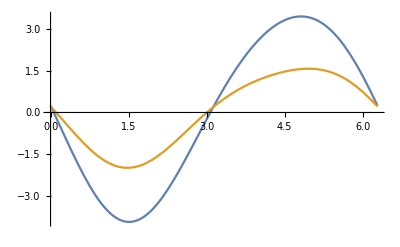

```mathematica
Plot[{pvx10[ theta2,myt2,nmax],pv10[1,1,theta2,myt2]},{theta2,0,2Pi}]
```

```mathematica
Plot[{pvx10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvx20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]],pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic]
```

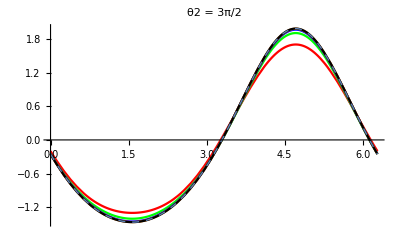

```mathematica
myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=2;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=3;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=4;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=5;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
plot[nmax+1]=Plot[pv20[1,1,myt2,theta2],{theta2,0,2Pi},PlotStyle->{Dashed,Thick}];
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]
```